```mathematica
gaussian=Exp[-(1/(4 D)) ((x-xp)^2/(t-tp))];
```

```mathematica
ⅇ^(-(x-xp)^2/(4 D (t-tp)))
```

ⅇ^(-(x-xp)^2/(4 D (t-tp)))

```mathematica
D[gaussian,xp]
```

(ⅇ^(-(x-xp)^2/(4 D (t-tp))) (x-xp))/(2 D (t-tp))

```mathematica
-(ⅇ^(-(α (x-x')^2)/(4 ν^2 (t-t'))) α (1-(0&)) (x-x'))/(2 ν^2 (t-t'))
```

```mathematica
Simplify[D[gaussian,{xp,2}]]
```

(ⅇ^(-(x-xp)^2/(4 D (t-tp))) (-2 D (t-tp)+(x-xp)^2))/(4 D^2 (t-tp)^2)

```mathematica
(*Clear symbols and define R^2 for convenience*)ClearAll[x,y,b,d,t,R];
R=Sqrt[(x-b)^2+(y-b)^2];

(*Define the integral I*)
I=Integrate[(1/t^5)*Exp[-(R^2)/(4 D t)]*((x-b)^2-2 D t)*((y-b)^2-2 D t),{t,0,Infinity},Assumptions->{D>0,R>0}];
```

ClearAll::wrsym: Symbol D is Protected.

Set::wrsym: Symbol ⅈ is Protected.

```mathematica
ClearAll[x,y,b,d,t,R];
R[b_]=(x-b)^2+(y-b)^2
```

(-b+x)^2+(-b+y)^2

```mathematica
Ires[b_]=Integrate[(1/t^5)*Exp[-R[b]/(4 D t)]*((x-b)^2-2 D t)*((y-b)^2-2 D t),{t,0,Infinity},Assumptions->{D>0,R>0}]
```

ConditionalExpression[(256 D^4 (6 (b-x)^2 (b-y)^2+1/4 R[b] (-4 (2 b^2+x^2+y^2-2 b (x+y))+R[b])))/R[b]^4, Re[R[b]]>0]

```mathematica
res=FullSimplify[Ires,Assumptions->{D>0,R>0}]
```

(192 D^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/((2 b^2+x^2+y^2-2 b (x+y))^4)

```mathematica
Together[res]
```

(192 D^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/((2 b^2-2 b x+x^2-2 b y+y^2)^4)

```mathematica
Ires[b]+Ires[a]
```

(192 D^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/((2 b^2+x^2+y^2-2 b (x+y))^4)[a]+(192 D^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/((2 b^2+x^2+y^2-2 b (x+y))^4)[b]

```mathematica
FullSimplify[Ires[b]+Ires[a]]
```

(192 D^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/((2 b^2+x^2+y^2-2 b (x+y))^4)[a]+(192 D^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/((2 b^2+x^2+y^2-2 b (x+y))^4)[b]

```mathematica
196/64
```

49/16

```mathematica
ClearAll[x,y,b];

(*Define your expression*)
expr=((2 b^2-4 b x+x^2+2 x y-y^2)*(2 b^2-4 b y-x^2+2 x y+y^2))/((x-b)^2+(y-b)^2)^4;

(*Ask Mathematica to simplify*)
simplExpr=FullSimplify[expr,Assumptions->{(x-b)^2+(y-b)^2!=0}];

simplExpr
```

((2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/(((b-x)^2+(b-y)^2)^4)

```mathematica
Pi
```

π

```mathematica
gaussian=Exp[-(1/(4 d)) ((x-xp)^2/(t-tp))]/(sqrt[4 Pi d(t-tp)])
```

(ⅇ^(-(x-xp)^2/(4 d (t-tp))))/sqrt[4 d π (t-tp)]

```mathematica
D[gaussian,tp]
```

-(ⅇ^(-(x-xp)^2/(4 d (t-tp))) (x-xp)^2)/(4 d (t-tp)^2 sqrt[4 d π (t-tp)])+(4 d ⅇ^(-(x-xp)^2/(4 d (t-tp))) π sqrt'[4 d π (t-tp)])/sqrt[4 d π (t-tp)]^2

```mathematica
D[gaussian,tp]-d^2*D[gaussian,{xp,2}]
```

-(d^2 (-(ⅇ^(-(x-xp)^2/(4 d (t-tp))))/(2 d (t-tp))+(ⅇ^(-(x-xp)^2/(4 d (t-tp))) (x-xp)^2)/(4 d^2 (t-tp)^2)))/sqrt[4 d π (t-tp)]-(ⅇ^(-(x-xp)^2/(4 d (t-tp))) (x-xp)^2)/(4 d (t-tp)^2 sqrt[4 d π (t-tp)])+(4 d ⅇ^(-(x-xp)^2/(4 d (t-tp))) π sqrt'[4 d π (t-tp)])/sqrt[4 d π (t-tp)]^2

```mathematica
Simplify[D[gaussian,tp]-d^2*D[gaussian,{xp,2}]]
```

(ⅇ^(-(x-xp)^2/(4 d (t-tp))) ((2 d^2 (t-tp)-(x-xp)^2-d (x-xp)^2) sqrt[4 d π (t-tp)]+16 d^2 π (t-tp)^2 sqrt'[4 d π (t-tp)]))/(4 d (t-tp)^2 sqrt[4 d π (t-tp)]^2)

```mathematica
(* ::Package::*)(*1) Define the operator L[u(x)]=u''(x)-k^2 u(x).You can customize this to any ODE or PDE operator you wish.*)ClearAll[Lop];
Lop[u_,x_,k_]:=D[u,{x,2}]-k^2 u;

(*2) Define the candidate Green's function G(x,y) as a piecewise function.For demonstration,a known G(x,y) on[0,pi] for L[u]=u''(x)-k^2 u(x) with Dirichlet boundary conditions at 0 and pi.*)
ClearAll[G];
G[x_,y_,k_]:=Piecewise[{{(1/(k Sin[k π])) Sin[k x] Sin[k (π-y)],x<y},{(1/(k Sin[k π])) Sin[k y] Sin[k (π-x)],x>y}}];

(*3) Define a checking function.We check two main things:i) L[G(x,y)]==DiracDelta[x-y]  (in the sense of distributions) ii) Boundary conditions:G(0,y)==0 and G(pi,y)==0,for all y in (0,pi).We use symbolic manipulations to get as close as possible to verifying these conditions.For rigorous delta-checks in symbolic form,we'll rely on known distribution identities and possibly look at the limit behavior near x=y.*)

ClearAll[checkGreensFunction];
checkGreensFunction[Lop_,G_,{x_,xMin_,xMax_},y_,k_]:=Module[{eq,bcLeft,bcRight},(*3a) Symbolic difference L[G(x,y)]-DiracDelta[x-y].*)eq=FullSimplify[Lop[G[x,y,k],x,k]-DiracDelta[x-y],Assumptions->{xMin<x<xMax,xMin<y<xMax,k>0}];
(*3b) Evaluate boundary conditions G(x,y) at x=xMin (0) and x=xMax (pi).*)bcLeft=FullSimplify[G[xMin,y,k],Assumptions->{xMin<y<xMax,k>0}];
bcRight=FullSimplify[G[xMax,y,k],Assumptions->{xMin<y<xMax,k>0}];
Print["--- Checking L[G(x,y)] - DiracDelta[x-y] ---"];
Print["Expression = ",eq];
Print["--- Checking boundary conditions ---"];
Print["G(0, y)   = ",bcLeft];
Print["G(pi, y)  = ",bcRight];
Return[eq]];

(*4) Test the checkGreensFunction with the operator Lop and the proposed G.We'll examine the symbolic result,although we should expect delta-function and distributional behavior in the derivative at x=y.*)
checkGreensFunction[Lop,G,{x,0,π},y,k]
```

--- Checking L[G(x,y)] - DiracDelta[x-y] ---

Expression = -DiracDelta[x-y]-k^2 (Piecewise[{{(Csc[k π] Sin[k x] Sin[k (π-y)])/k, x<y}, {(Csc[k π] Sin[k (π-x)] Sin[k y])/k, x>y}, {0, True}}])+(Piecewise[{{-k Csc[k π] Sin[k x] Sin[k (π-y)], x<y}, {-k Csc[k π] Sin[k (π-x)] Sin[k y], x>y}, {0, True}}])

--- Checking boundary conditions ---

G(0, y)   = 0

G(pi, y)  = 0

-DiracDelta[x-y]-k^2 (Piecewise[{{(Csc[k π] Sin[k x] Sin[k (π-y)])/k, x<y}, {(Csc[k π] Sin[k (π-x)] Sin[k y])/k, x>y}, {0, True}}])+(Piecewise[{{-k Csc[k π] Sin[k x] Sin[k (π-y)], x<y}, {-k Csc[k π] Sin[k (π-x)] Sin[k y], x>y}, {0, True}}])

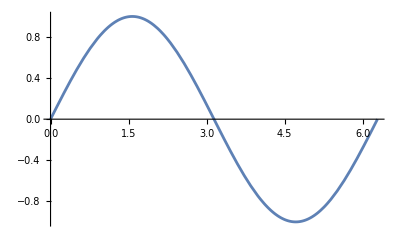

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

```mathematica
ContourPlot[( x^2+y^2-2),{x,-2,2},{y,-2,2},Contours->10,PlotLabel->"Contour of x^2 + y^2"]
```

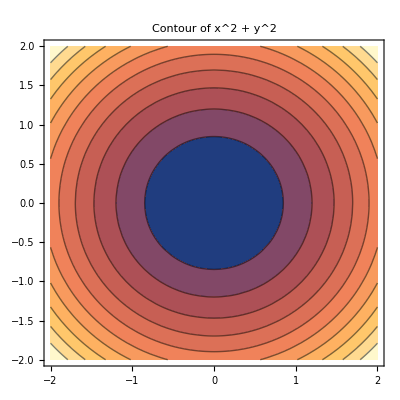
```mathematica
-Graphics-
(y-x)^4
```

-Graphics-

(-x+y)^4

```mathematica
simplExpr(y-x)^4
```

((-x+y)^4 (2 b^2-4 b x+x^2+2 x y-y^2) (2 b^2-x^2-4 b y+2 x y+y^2))/(((b-x)^2+(b-y)^2)^4)

```mathematica
Expand[(y-x)^4]
```

x^4-4 x^3 y+6 x^2 y^2-4 x y^3+y^4

(x-y)^4

```mathematica
Simplify[Expand[(x^{2}+y^{2})^{2}-2(y-x)^{4}]]
```

{-x^4+8 x^3 y-10 x^2 y^2+8 x y^3-y^4}

```mathematica
Func[x_,y_]=(x^2+y^2-2(y-x)^4)/(x^2+y^2)^4
```

(x^2+y^2-2 (-x+y)^4)/((x^2+y^2)^4)

```mathematica
Func[1,2]
```

3/625

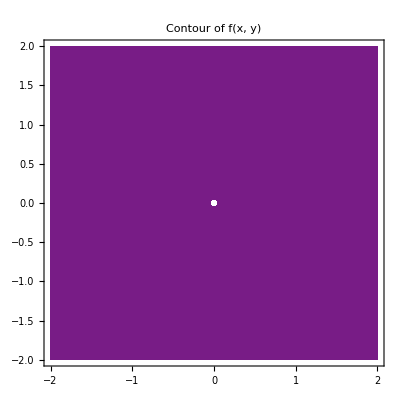

```mathematica
ContourPlot[Func[x,y],{x,-2,2},{y,-2,2},PlotRange->All,RegionFunction->(Norm[{#1,#2}]>0.05&),Contours->20,ColorFunction->"Rainbow",PlotLabel->"Contour of f(x, y)"]
```

```mathematica
CountourPlot[(x^2+y^2-2 (y-x))/(x^2+y^2)^4,{x,-2,2},{y,-2,2},PlotRange->All,RegionFunction->(Norm[{#1,#2}]>0.1&),(*Exclude radius 0.1*)PlotPoints->50,(*Increase sampling resolution*)MaxRecursion->3,(*Allows deeper adaptive sampling*)PlotLabel->"f(x, y)"]
```

```mathematica
CountourPlot[(x^2+y^2-2 (-x+y))/((x^2+y^2)^4),{x,-2,2},{y,-2,2},PlotRange->All,RegionFunction->(Norm[{#1,#2}]>0.1&),PlotPoints->50,MaxRecursion->3,PlotLabel->"f(x, y)"]
```

CountourPlot[(x^2+y^2-2 (-x+y))/((x^2+y^2)^4),{x,-2,2},{y,-2,2},PlotRange→All,RegionFunction→(Norm[{#1,#2}]>0.1&),PlotPoints→50,MaxRecursion→3,PlotLabel→f(x, y)]

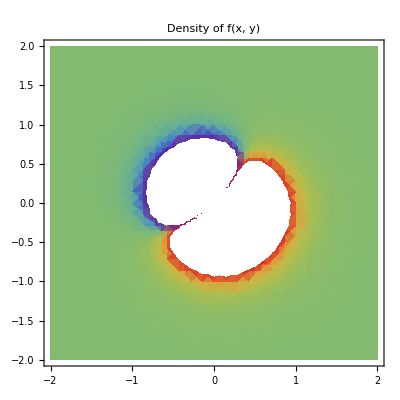

```mathematica
DensityPlot[(x^2+y^2-2 (y-x))/(x^2+y^2)^4,{x,-2,2},{y,-2,2},RegionFunction->(Norm[{#1,#2}]>0.1&),PlotRange->{-5,5},(*clip or use All*)ColorFunction->"Rainbow",PlotLabel->"Density of f(x, y)"]
```

```mathematica
Plot3D[(x^2+y^2-2(y-x)^4)/(x^2+y^2)^4,{x,-2,2},{y,-2,2},RegionFunction->(Norm[{#1,#2}]>0.1&),ScalingFunctions->"Log",(*log scale for the z-axis*)PlotPoints->50]
```

-Graphics3D-

```mathematica
ContourPlot[(x^2+y^2-2 (y-x)^4)/(x^2+y^2)^4,{x,-2,2},{y,-2,2},(*Exclude points near the origin (within radius 0.1)*)RegionFunction->(Norm[{#1,#2}]>0.1&),(*Let Mathematica automatically determine vertical range,but clip extreme spikes to keep contour lines interpretable*)PlotRange->{-10,10},(*Increase resolution and allow adaptive refinement*)PlotPoints->50,MaxRecursion->3,(*Define how many contours you want and which color scheme to use*)Contours->20,ColorFunction->"Rainbow",PlotLabel->"Contour of f(x, y)"]
```

-Graphics-

```mathematica
Solve[(x^2+y^2)^2-2(x-y)^4==0]
```

{{y→2 x-√2 x-√(5 x^2-4 √2 x^2)},{y→2 x-√2 x+√(5 x^2-4 √2 x^2)},{y→2 x+√2 x-√(5 x^2+4 √2 x^2)},{y→2 x+√2 x+√(5 x^2+4 √2 x^2)}}

```mathematica
Plot[(x^2+y^2)^2-2(x-y)^4,{x,y}]
```

Plot::pllim: Range specification {x,y} is not of the form {x, xmin, xmax}.

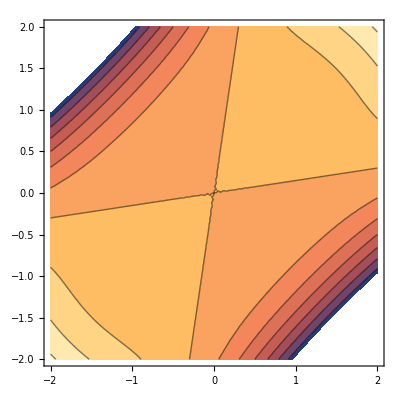

```mathematica
ContourPlot[(x^2+y^2)^2-2 (x-y)^4,{x,-2,2},{y,-2,2}]
```

```mathematica
(x^{2}+y^{2})^{2}-2(y-x)^{4}
```

```mathematica
(ρ^(1))[x_,t_]=(mu*rho0)/(8 Sqrt[Pi])*Integrate[1/((D (t-t'))^(5/2))*Integrate[Exp[-((x-x')^2)/(4 D (t-t'))]*((x-x')^2-2 D (t-t'))*V[x',t'],{x',-Infinity,Infinity}],{t',-Infinity,t}]
```

(mu rho0 ∫_(-∞)^t (∫_(-∞)^∞ ⅇ^(-(x-x')^2/(4 D (t-t'))) V[x',t'] (-2 D (t-t')+(x-x')^2)ⅆ x')/(D (t-t'))^(5/2)ⅆ t')/(8 √π)

```mathematica
D[(ρ^(1))[x,t],{x,1}]
```

(mu rho0 ∫_(-∞)^t (∫_(-∞)^∞ (2 ⅇ^(-(x-x')^2/(4 D (t-t'))) V[x',t'] (x-x')-(ⅇ^(-(x-x')^2/(4 D (t-t'))) V[x',t'] (-2 D (t-t')+(x-x')^2) (x-x'))/(2 D (t-t')))ⅆ x')/(D (t-t'))^(5/2)ⅆ t')/(8 √π)

```mathematica
(*Clear all symbols to avoid shadowing*)ClearAll["Global`*"];

(*Define the integral as a function of x,y,D*)
integrand[x_,y_,D_,t_]:=(1/t^5) Exp[-(x^2+y^2)/(4 D t)] (x^2-2 D t) (y^2-2 D t)

theIntegral[x_,y_,D_]:=Integrate[integrand[x,y,D,t],{t,0,Infinity},Assumptions->{D>0,x^2+y^2>0}]

(*Perform the integral and simplify the result*)
result[x_,y_,D_]:=FullSimplify[theIntegral[x,y,D],Assumptions->{D>0,x^2+y^2>0}]

(*Example usage:symbolic result*)
symbolicResult=result[x,y,D]

(*Optionally,you can substitute specific numeric values for x,y,D to get a numeric result.*)
testNumeric=result[1,2,1.0]//N
```

-(192 D^4 (x^4-6 x^2 y^2+y^4))/((x^2+y^2)^4)

2.1504

```mathematica
196/64
```

49/16

```mathematica
Hello
```

Hello